```mathematica
permutation = RandomSample[Range[1, 255]]; 
p = Join[permutation, permutation]; (*repeat it to avoid overflow*)
repeat = 255;

fade[t_] := t*t*t*(t*(t*6-15)+10); (* THE FADE FUNCTION >:) *)
inc[n_] := Module[{num = n+1}, If[repeat >0, num = Mod[num, repeat]]];

grad[hash_, x_, y_, z_] := Module[{hashy = Min[hash,15 ]}, 
Which[
hashy==0, x+y,
hashy==1, -x+y,
hashy==2, x-y,
hashy==3, -x-y,
hashy==4, x+z,
hashy==5, -x+z,
hashy==6, x-z,
hashy==7, -x-z,
hashy==8, y+z,
hashy==9, -y+z,
hashy==10, y-z,
hashy==11,-y-z,
hashy==12,y+x,
hashy==13,-y+z,
hashy==14,y-x,
hashy==15,-y-z]];
lerp[a_,b_,x_] :=a+x*(b-a);

perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 254], yi = Min[Floor[b], 254], zi = Min[Floor[c], 254], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];  
xf = x-Floor[x];yf = y-Floor[y];zf = z-Floor[z]; 
u = fade[xf]; v = fade[yf]; w = fade[zf];
aaa =p[[p[[p[[        xi   +1]]+yi+1]]+        zi    +1]]; aba = p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]]; aab=p[[p[[p[[         xi   +1]]+yi+1]]+inc[zi]+1]]; abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]]; baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+          zi  +1]]; bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]]; bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]]; bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1 = lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf], u];
x2 = lerp[grad[aba, xf, yf-1, zf], grad[bba, xf-1, yf-1, zf],u];
y1 = lerp[x1, x2, v];
x1 = lerp[grad[aab, xf, yf, zf-1], grad[bab, xf-1, yf, zf-1], u];
x2 = lerp[grad[abb, xf, yf-1, zf-1], grad[abb, xf, yf-1, zf-1], u];
y2 = lerp[x1, x2, v];
Rescale[lerp[y1, y2, w], {-1.2, 1.2}]];

octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0, frequency=1,amplitude=1,maxValue=0},
total = perlin[x*frequency,y*frequency,z*frequency]*amplitude + Total[Table[maxValue+= amplitude;amplitude*=persistence;frequency*=2;perlin[x*frequency,y*frequency,z*frequency]*amplitude, {i,octaves-1}]]; total/maxValue];
```

```mathematica
ex = Table[octavePerlin[RandomInteger[{0, 10}], RandomInteger[{0, 10}], RandomReal[{0, 10}], octaves, persistence], 100000];
Max[ex]
Min[ex]
Mean[ex]
```

0.74665

0.400067

0.568105

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=
 Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren},
  
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[clamp[x_, 2],yStart_,yEnd_,width_]:=AppendTo[roads,{x,yStart,x,yEnd,width}];
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=AppendTo[roads,{xStart,y,xEnd,y,width}];
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];
  
  stack={{0,0,worldWidth,worldHeight}};
  
  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
    Psplit=smoothstep[lowCutoff,highCutoff,n]*2;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  roads
  ]
```

```mathematica
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=

 Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False, sizeFactor},
  
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{Max[x, 1],Max[yStart, 1],Max[x, 1],yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{Max[xStart, 1],Max[y, 1],xEnd,Max[y, 1],width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];
  
  stack={{0,0,worldWidth,worldHeight}};
  
  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
sizeFactor=Min[(R[[3]]/minBlock)+(R[[4]]/minBlock),2];
(*sizeFactor=smoothstep[1,2,Min[R[[3]]/minBlock,R[[4]]/minBlock]];*)
    Psplit=smoothstep[lowCutoff,highCutoff,n]*sizeFactor;
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]
```

## HEHEHEHAAWHAWHAHW

```mathematica
worldWidth=100;
worldHeight=100;
minBlock=12;
maxJitter=5;
roadWidth=2;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;

roadsCoords = generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff]

MapGrid = Table[0, {x, worldWidth}, {y, worldHeight}];
(*For[i=1, i<=Length[roadsCoords], i++,
Module[{x1=roadsCoords[[]][[1]], x2=roadsCoords[[3]],y1=roadsCoords[[2]],y2=roadsCoords[[4]], width=roadsCoords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->"R"],MapGrid=ReplacePart[MapGrid,{i_,y1}/;x1<i<x2->"R"] ]]];*)
roadPutter[Coords_] := Module[{x1=Coords[[1]]//Floor, x2=Coords[[3]]//Floor,y1=Coords[[2]]//Floor,y2=Coords[[4]]//Floor, width=Coords[[5]]},If[x1==x2,MapGrid=ReplacePart[MapGrid,{x1,j_}/;y1<j<y2->1],MapGrid=ReplacePart[MapGrid,{i_,y1}/;x1<i<x2->1] ]];
roadPutter/@roadsCoords;
ArrayPlot@MapGrid
```

{{1,50.6348,100,50.6348,2},{48.3994,1,48.3994,50.6348,2},{49.0536,50.6348,49.0536,100.,2},{1,29.4756,48.3994,29.4756,2},{73.1545,1,73.1545,50.6348,2},{1,77.8831,49.0536,77.8831,2},{75.3706,50.6348,75.3706,100.,2},{19.3332,1,19.3332,29.4756,2},{48.3994,25.125,73.1545,25.125,2},{73.1545,28.3966,100.,28.3966,2},{20.134,50.6348,20.134,77.8831,2},{49.0536,73.9702,75.3706,73.9702,2},{75.3706,73.7388,100.,73.7388,2},{19.3332,15.0562,48.3994,15.0562,2},{48.3994,13.125,73.1545,13.125,2},{48.3994,37.125,73.1545,37.125,2},{73.1545,16.3966,100.,16.3966,2},{35.8024,50.6348,35.8024,77.8831,2},{61.0536,73.9702,61.0536,100.,2},{75.3706,86.3904,100.,86.3904,2}}

-Graphics-

```mathematica
findZeroBlocks[grid_]:=Module[{blocks={},rowCount,colCount,visited,markBlock,i,j},
  {rowCount,colCount}=Dimensions[grid];
  visited=ConstantArray[False,{rowCount,colCount}];
  
  markBlock[startRow_,startCol_]:=Module[{endRow=startRow,endCol=startCol},
    (* Find the end column of the block *)
    While[endCol<=colCount&&grid[[startRow,endCol]]==0&&!visited[[startRow,endCol]],
      endCol++
    ];
    endCol--;
    
    (* Find the end row of the block *)
    While[endRow<=rowCount&&
      AllTrue[Range[startCol,endCol],(grid[[endRow,#]]==0&&!visited[[endRow,#]]) &],
      endRow++
    ];
    endRow--;
    
    (* Mark the block as visited *)
    Do[
      visited[[r,c]]=True,
      {r,startRow,endRow},{c,startCol,endCol}
    ];
    
    (* Add block coordinates to the list *)
    AppendTo[blocks,{{startRow,startCol},{endRow,endCol}}];
  ];
  
  Do[
    If[grid[[i,j]]==0&&!visited[[i,j]],
      markBlock[i,j]
    ],
    {i,rowCount},{j,colCount}
  ];
  
  blocks
]

(* Example usage with MapGrid *)
findZeroBlocks[MapGrid]
```

{{{1,1},{1,100}},{{2,1},{18,28}},{{2,30},{47,49}},{{2,51},{19,76}},{{2,78},{48,100}},{{19,1},{100,1}},{{20,2},{47,14}},{{20,16},{47,28}},{{21,51},{34,76}},{{36,51},{48,76}},{{49,2},{72,12}},{{49,14},{72,24}},{{49,26},{72,36}},{{49,38},{72,49}},{{49,100},{100,100}},{{50,51},{74,72}},{{50,74},{60,99}},{{62,74},{74,99}},{{74,2},{100,15}},{{74,17},{100,27}},{{74,29},{100,49}},{{76,51},{100,72}},{{76,74},{100,85}},{{76,87},{100,99}},{{100,16},{100,16}},{{100,28},{100,28}},{{100,50},{100,50}},{{100,73},{100,73}},{{100,86},{100,86}}}

```mathematica
mg={{0, 0, 0, 1, 0, 0},{0, 0, 0, 1, 0, 0},{1,1,1,1,1,1},{0,1,0,0,0,0},{0,1,0,0,0,0}};
mg//Grid
visited=mg;
worldWidth=6;
worldHeight=5;
zeroBlocks={};
findDownRight[x_,y_,grid_]:=Module[{i=x,j=y},If[visited[[x,y]]==0,Until[grid[[i,j]]==1||i>worldWidth,Echo[i++];Print[i, j, grid[[i,j]]]];Echo[i--];Until[grid[[i,j]]==1||j>worldHeight,j++];j--;ReplacePart[visited,{a_,b_}/;x<a<i&&y<b<j->1];AppendTo[zeroBlocks,{x, y, i, j}]]];
findDownRight[1, 1, mg]
```

0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1
0 | 1 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0

1

210

2

311

3

{{1,1,2,3}}

### failure

186.623

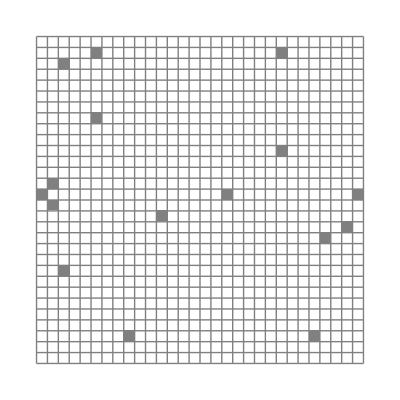

```mathematica
roadOctave = RandomInteger[{3, 4}]; roadPers = RandomReal[{0.45, 0.55}];

classifyRoadTile[val_]:=Which[val>0.47 && val < 0.53,"road", True,"background"];
tileColors=<|"background"->White,"road"->Gray|>;
tileToNumber=AssociationThread[Keys[tileColors],Range[Length[tileColors]]];
(*noiseMap = SparseArray*)
z = RandomReal[{0, 255}]
noiseMap=Table[octavePerlin[x,y, z, roadOctave, roadPers],{x,1,30},{y,1,30}];
tileMap=Map[classifyRoadTile,noiseMap,{2}];
numericGrid=Map[tileToNumber,tileMap,{2}];
(*numericGrid[[All,mid]]=1;*)


visualizeTileMap[tileMap_]:=Module[{tileColors=<|"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>,tileNums,colorRules},tileNums=AssociationThread[Keys@tileColors,Range@Length@tileColors];
colorRules=Thread[Values@tileNums->Values@tileColors];
ArrayPlot[tileNums/@tileMap,ColorRules->colorRules,Frame->False,Mesh->True,MeshStyle->Gray]];

ArrayPlot[numericGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False,Mesh->True,MeshStyle->Gray]
```

```mathematica
octaves = RandomInteger[{3, 5}]; persistence = RandomReal[{0.4, 0.6}]; size = 10; scale = 5;classifyTile[v_] := Which[
v>0.45, "building",
v <= 0.45, "park",
True,"road"];
classifyMap[noiseMap_]:=Map[classifyTile,noiseMap,{2}]

generateNoiseMap[size_, octaves_, persistence_, scale_]:=Table[octavePerlin[x/scale, y/scale, RandomReal[0, 255], octaves, persistence], {x, 0, size-1}, {y, 0, size-1}]

tileColors=<|"empty"->White,"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>;

tileToNumber=AssociationThread[Keys[tileColors],Range[Length[tileColors]]];
numberToColor=Values[tileColors];
visualizeTileMap[tileMap_]:=ArrayPlot[tileToNumber/@tileMap,ColorRules->Thread[Range[Length[numberToColor]]->numberToColor],Frame->False,Mesh->True,MeshStyle->Gray]

noiseMap=generateNoiseMap[size,octaves,persistence,scale]
tileMap=classifyMap[noiseMap];
(*visualizeTileMap[tileMap]*)
```

```mathematica
classifyTile[val_]:=Which[val>0.61,"building",val< 0.61,"park",True,"road"];

generateNoiseMap[size_,oct_,pers_,scale_]:=Module[{z=RandomReal[{0,255}]},Table[octavePerlin[x/scale,y/scale,z,oct,pers],{x,0,size-1},{y,0,size-1}]];

visualizeTileMap[tileMap_]:=Module[{tileColors=<|"road"->Gray,"building"->Darker[Red],"park"->LightGreen|>,tileNums,colorRules},tileNums=AssociationThread[Keys@tileColors,Range@Length@tileColors];
colorRules=Thread[Values@tileNums->Values@tileColors];
ArrayPlot[tileNums/@tileMap,ColorRules->colorRules,Frame->False,Mesh->True,MeshStyle->Gray]];

(*---demo----------------------------------------------------------*)
(*SeedRandom[123];*)
size=20;oct=4;pers=0.5;scale=5; octaves = RandomInteger[{3, 4}]; persistence = RandomReal[{0.4, 0.5}];

noiseMap=Table[octavePerlin[x*10,y*10, RandomReal[{0, 255}], octaves, persistence],{x,1,10},{y,1,10}]

tileMap=Map[classifyTile,noiseMap,{2}];
numericGrid=Map[tileToNumber,tileMap,{2}];
ArrayPlot[numericGrid,ColorRules->Thread[Values[tileToNumber]->Values[tileColors]],Frame->False,Mesh->True,MeshStyle->Gray]
```

## BLEAI

I want to implement a recursive subdivision road generator where it: Start with a single rectangle representing the whole map; repeatedly split it in half and draw a road along each split until every rectangle is smaller than your chosen “city block” size. However, I want to add some randomness to it since I have already implemented a perlin noise generator: perlin[x, y, z] and an octave perlin noise generator: octavePerlin[x, y, z, octaves, persistence]. I want to use it so that it can define some places to be more sparse with less road intersections while others are more dense with road intersection. Here is some pseudocode for the original road generator: Input:  worldWidth, worldHeight, minBlock, maxJitter, roadWidth
stack ← [ Rectangle(0,0, worldWidth, worldHeight) ]
roads ← ∅

while stack not empty:
    R ← pop(stack)
    
    if R.width < 2*minBlock OR R.height < 2*minBlock:
        continue   // already small enough; stop recursing

    // Decide split direction: favour the longer axis
    if R.width > R.height:
        dir ← "vertical"
    else if R.height > R.width:
        dir ← "horizontal"
    else:
        dir ← randomChoice("vertical", "horizontal")

    // Choose split position with optional jitter
    if dir = "vertical":
        xSplit ← R.x + R.width/2 + randomUniform(-maxJitter, +maxJitter)
        // Clamp so both children ≥ minBlock wide
        xSplit ← clamp(xSplit, R.x + minBlock, R.x + R.width - minBlock)
        roads.add( VerticalRoad(xSplit, R.y, R.y + R.height, roadWidth) )
        // Push the two child rectangles
        stack.push( Rectangle(R.x, R.y,   xSplit - R.x, R.height) )
        stack.push( Rectangle(xSplit, R.y, R.x + R.width - xSplit, R.height) )
    else:             // horizontal split
        ySplit ← R.y + R.height/2 + randomUniform(-maxJitter, +maxJitter)
        ySplit ← clamp(ySplit, R.y + minBlock, R.y + R.height - minBlock)
        roads.add( HorizontalRoad(R.x, ySplit, R.x + R.width, ySplit, roadWidth) )
        stack.push( Rectangle(R.x, R.y, R.width, ySplit - R.y) )
        stack.push( Rectangle(R.x, ySplit, R.width, R.y + R.height - ySplit) )

return roads            // a list of axis-aligned line segments
here is a possible idea of how to implement the perlin noise:Input: worldW, worldH, minBlock, maxJitter, roadW,
       noiseFreq, lowCutoff, highCutoff      // new

Noise(x,z) = perlin2D(x*noiseFreq, z*noiseFreq)  // returns 0–1

stack ← [ Rectangle(0,0, worldW, worldH) ]
roads ← ∅

while stack not empty:
    R ← pop(stack)

    // --- decide if we even want to split here -------------
    n ← Noise(R.centreX, R.centreY)          // 1 sample → cheap
    Psplit ← smoothstep(lowCutoff, highCutoff, n)
    if randomUniform(0,1) > Psplit:          // suburban zone
        continue                              // ← no further cuts
    // ------------------------------------------------------

    if R.width < 2*minBlock OR R.height < 2*minBlock:
        continue

    dir ← pickAxis(R)
    if dir = "vertical":
        xSplit ← R.x + R.width/2 + jitter(maxJitter)
        xSplit ← clamp(xSplit, R.x + minBlock, R.x + R.width - minBlock)
        addVerticalRoad(...)
        pushChildren(...)
    else:
        ... same for horizontal ...

generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=
 Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren},
  
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=AppendTo[roads,{x,yStart,x,yEnd,width}];
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=AppendTo[roads,{xStart,y,xEnd,y,width}];
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];
  
  stack={{0,0,worldWidth,worldHeight}};
  
  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
    Psplit=smoothstep[lowCutoff,highCutoff,n];
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  roads
  ]

worldWidth=100;
worldHeight=100;
minBlock=10;
maxJitter=5;
roadWidth=2;
noiseFreq=0.1;
lowCutoff=0.2;
highCutoff=0.8;

generateRoads[worldWidth,worldHeight,minBlock,maxJitter,roadWidth,noiseFreq,lowCutoff,highCutoff]Wolfram

Whats the best way to iterate through a list where each iteration, I use the values inside each element for something

To iterate through a list and use the values inside each element, you can use several built-in functions in Wolfram Language, such as Mappaclet:ref/Maphttps://reference.wolfram.com/language/ref/Map.html, Dopaclet:ref/Dohttps://reference.wolfram.com/language/ref/Do.html, Tablepaclet:ref/Tablehttps://reference.wolfram.com/language/ref/Table.html, or Scanpaclet:ref/Scanhttps://reference.wolfram.com/language/ref/Scan.html. Here are examples of each approach: 
"Using Map"
list={{1,2},{3,4},{5,6}};
Map[function,list]Wolfram
function will be applied to each element of list. This is useful for applying a transformation to each element. 
"Using Do"
list={{1,2},{3,4},{5,6}};
Do[
  (* Your code using i, j here *)
  Print[i+j],
  {i,list}
]Wolfram
Dopaclet:ref/Dohttps://reference.wolfram.com/language/ref/Do.html allows for more procedural code where you can perform multiple operations using i. 
"Using Table"
list={{1,2},{3,4},{5,6}};
Table[
  i+j,
  {i,list}
]Wolfram
Tablepaclet:ref/Tablehttps://reference.wolfram.com/language/ref/Table.html is useful for building a new list from the elements of the original list. 
"Using Scan"
list={{1,2},{3,4},{5,6}};
Scan[
  (Print[#];) &,
  list
]Wolfram
Scanpaclet:ref/Scanhttps://reference.wolfram.com/language/ref/Scan.html is used when you want to perform an operation on each element without producing a new list. It is similar to Mappaclet:ref/Maphttps://reference.wolfram.com/language/ref/Map.html, but it doesn't return a list of results.

Choose the approach that best fits your needs. If you want to modify or transform the list, Mappaclet:ref/Maphttps://reference.wolfram.com/language/ref/Map.html or Tablepaclet:ref/Tablehttps://reference.wolfram.com/language/ref/Table.html are typically best. For purely procedural operations without returning a result, Dopaclet:ref/Dohttps://reference.wolfram.com/language/ref/Do.html or Scanpaclet:ref/Scanhttps://reference.wolfram.com/language/ref/Scan.html might be more appropriate.

How do I make the generate roads functions have at least one road

To ensure that the generateRoads function always produces at least one road, you can modify the logic to guarantee that at least one split occurs. Here is an approach to achieve this:

1. Add a Flag: Introduce a flag or a counter to track whether at least one road has been added.
2. Force Split: If the function completes without adding any roads, you can force a split on the initial rectangle.

Here is how you can modify the function: 
generateRoads[worldWidth_,worldHeight_,minBlock_,maxJitter_,roadWidth_,noiseFreq_,lowCutoff_,highCutoff_]:=
 Module[{stack,roads={},noise,smoothstep,jitter,clamp,pickAxis,addVerticalRoad,addHorizontalRoad,pushChildren,roadAdded=False},
  
  noise[x_,z_]:=octavePerlin[x*noiseFreq,z*noiseFreq,0,4,0.5];
  
  smoothstep[low_,high_,x_]:=Module[{t},t=Clip[(x-low)/(high-low),{0,1}]; t*t*(3-2*t)];
  
  jitter[max_]:=RandomReal[{-max,max}];
  
  clamp[val_,min_,max_]:=Min[Max[val,min],max];
  
  pickAxis[R_]:=If[R[[3]]>R[[4]],"vertical","horizontal"];
  
  addVerticalRoad[x_,yStart_,yEnd_,width_]:=(AppendTo[roads,{x,yStart,x,yEnd,width}]; roadAdded=True);
  
  addHorizontalRoad[xStart_,y_,xEnd_,width_]:=(AppendTo[roads,{xStart,y,xEnd,y,width}]; roadAdded=True);
  
  pushChildren[R_,xSplit_,ySplit_,dir_]:=
   If[dir=="vertical",
    AppendTo[stack,{R[[1]],R[[2]],xSplit-R[[1]],R[[4]]}];
    AppendTo[stack,{xSplit,R[[2]],R[[3]]+R[[1]]-xSplit,R[[4]]}],
    AppendTo[stack,{R[[1]],R[[2]],R[[3]],ySplit-R[[2]]}];
    AppendTo[stack,{R[[1]],ySplit,R[[3]],R[[4]]+R[[2]]-ySplit}]
    ];
  
  stack={{0,0,worldWidth,worldHeight}};
  
  While[Length[stack]>0,
   Module[{R,n,Psplit,dir,xSplit,ySplit},
    R=First[stack];
    stack=Rest[stack];
    
    n=noise[R[[1]]+R[[3]]/2,R[[2]]+R[[4]]/2];
    Psplit=smoothstep[lowCutoff,highCutoff,n];
    If[RandomReal[]>Psplit,Continue[]];
    
    If[R[[3]]<2*minBlock||R[[4]]<2*minBlock,Continue[]];
    
    dir=pickAxis[R];
    
    If[dir=="vertical",
     xSplit=clamp[R[[1]]+R[[3]]/2+jitter[maxJitter],R[[1]]+minBlock,R[[1]]+R[[3]]-minBlock];
     addVerticalRoad[xSplit,R[[2]],R[[2]]+R[[4]],roadWidth];
     pushChildren[R,xSplit,Null,dir],
     ySplit=clamp[R[[2]]+R[[4]]/2+jitter[maxJitter],R[[2]]+minBlock,R[[2]]+R[[4]]-minBlock];
     addHorizontalRoad[R[[1]],ySplit,R[[1]]+R[[3]],roadWidth];
     pushChildren[R,Null,ySplit,dir]
     ];
    ];
   ];
  
  (* Ensure at least one road is added *)
  If[!roadAdded,
   dir=pickAxis[{0,0,worldWidth,worldHeight}];
   If[dir=="vertical",
    xSplit=clamp[worldWidth/2+jitter[maxJitter],minBlock,worldWidth-minBlock];
    addVerticalRoad[xSplit,0,worldHeight,roadWidth],
    ySplit=clamp[worldHeight/2+jitter[maxJitter],minBlock,worldHeight-minBlock];
    addHorizontalRoad[0,ySplit,worldWidth,roadWidth]
    ];
   ];
  
  roads
  ]Wolfram
"Changes Made:"
• roadAdded Flag: A Boolean flag roadAdded is introduced to track if any road is added during the execution.
• Forced Split: At the end of the function, if no road has been added (roadAdded is Falsepaclet:ref/Falsehttps://reference.wolfram.com/language/ref/False.html), a forced split is performed on the entire map to ensure at least one road is added. The split direction is chosen based on the initial rectangle's dimensions. 
This ensures that the function will always return at least one road.

Can you explain the generateRoads function in specific detail?

Certainly! The generateRoads function is designed to generate a network of roads over a defined area, using recursive subdivision and Perlin noise to introduce randomness. Here's a detailed breakdown of its components: 
"Parameters"
• worldWidth, worldHeight: Define the dimensions of the rectangular area where roads will be generated.
• minBlock: The minimum size for a city block. Rectangles smaller than twice this size won't be split further.
• maxJitter: The maximum amount of random displacement applied to road splits, adding variability to the grid layout.
• roadWidth: The width of the roads being generated.
• noiseFreq, lowCutoff, highCutoff: Parameters controlling the Perlin noise function, which influences where roads will be placed.
"Function Components"
1. Initialization: 
   • stack: A list initialized with a single rectangle representing the whole area.
   • roads: An empty list that will store the generated roads.
   • The function also defines several utility functions to assist with the road generation process.
2. Utility Functions: 
   • noise[x, z]: Uses octavePerlin to generate a noise value at a given point, influencing road density.
   • smoothstep[low, high, x]: A smoothing function to interpolate between low and high based on x.
   • jitter[max]: Returns a random value within the range [-max, max] for adding variability.
   • clamp[val, min, max]: Restricts a value to be within the specified min and max.
   • pickAxis[R]: Chooses the axis (vertical or horizontal) to split based on rectangle dimensions.
3. Road Addition Functions: 
   • addVerticalRoad and addHorizontalRoad: Add a road to the roads list and set the roadAdded flag to Truepaclet:ref/Truehttps://reference.wolfram.com/language/ref/True.html.
4. Recursive Subdivision: 
   • The stack is processed in a loop, subdividing rectangles until they can't be split further.
   • For each rectangle:
     • Calculate the noise value at its center.
     • Use smoothstep to determine the probability of performing a split (Psplit).
     • If Psplit is not met or the rectangle is too small, it skips further processing.
     • Choose the split direction: vertical or horizontal.
     • Calculate the split position with optional jitter and clamp it to ensure both resulting rectangles are at least minBlock wide.
     • Add roads accordingly and push the resulting sub-rectangles onto the stack.
5. Ensure At Least One Road: 
   • After processing all rectangles, the function checks if any roads were added.
   • If not, it forces a split on the initial rectangle to ensure the roads list is not empty.
6. Output: 
   • The function returns a list of road segments, each defined by their start and end coordinates and width.
This function utilizes procedural generation techniques to create a road network that balances structured grid layouts with natural randomness, making it suitable for applications like city simulations or game environments.

## Archive

```mathematica
perlin[a_, b_, c_] := Module[{xi = Min[Floor[a], 255], yi = Min[Floor[b], 255], zi = Min[Floor[c], 255], aaa, aba, aab, abb, baa, bba, bab, bbb, x1, x2, y1, y2, x=a, y=b, z=c, xf, yf, zf, u, v, w},If[repeat> 0,{ x = Mod[a, repeat], y = Mod[b, repeat], z = Mod[c, repeat]}];
xf = x-Floor[x];
yf = y-Floor[y];
zf = z-Floor[z];
u = fade[xf]; v = fade[yf]; w = fade[zf]; 
aaa = p[[p[[p[[xi]]+yi]]+zi]];
x]
```

```mathematica
(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::*)(*Clean 3-D Perlin implementation+octave wrapper+tile visualiser*)(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::*)

(*---single-octave Perlin noise-----------------------------------*)
(*perlin[x_,y_,z_]:=Module[{xi,yi,zi,xf,yf,zf,u,v,w,(*lattice coords*)aaa,aba,aab,abb,baa,bba,bab,bbb,(*hashed corners*)x1,x2,y1,y2},{xi,yi,zi}=Mod[Floor@{x,y,z},repeat];
{xf,yf,zf}=FractionalPart/@{x,y,z};
{u,v,w}=fade/@{xf,yf,zf};
aaa=p[[p[[p[[xi+1]]+yi+1]]+zi+1]];
aba=p[[p[[p[[xi+1]]+inc[yi]+1]]+zi+1]];
aab=p[[p[[p[[xi+1]]+yi+1]]+inc[zi]+1]];
abb=p[[p[[p[[xi+1]]+inc[yi]+1]]+inc[zi]+1]];
baa=p[[p[[p[[inc[xi]+1]]+yi+1]]+zi+1]];
bba=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+zi+1]];
bab=p[[p[[p[[inc[xi]+1]]+yi+1]]+inc[zi]+1]];
bbb=p[[p[[p[[inc[xi]+1]]+inc[yi]+1]]+inc[zi]+1]];
x1=lerp[grad[aaa,xf,yf,zf],grad[baa,xf-1,yf,zf],u];
x2=lerp[grad[aba,xf,yf-1,zf],grad[bba,xf-1,yf-1,zf],u];
y1=lerp[x1,x2,v];
x1=lerp[grad[aab,xf,yf,zf-1],grad[bab,xf-1,yf,zf-1],u];
x2=lerp[grad[abb,xf,yf-1,zf-1],grad[bbb,xf-1,yf-1,zf-1],u];
y2=lerp[x1,x2,v];
Rescale[lerp[y1,y2,w],{-1,1}]            (* ∈[0,1]*)];*)

(*---multi-octave wrapper-----------------------------------------*)
(*octavePerlin[x_,y_,z_,octaves_,persistence_]:=Module[{total=0.,amp=1.,max=0.,freq=1.},Do[total+=perlin[x*freq,y*freq,z*freq]*amp;
max+=amp;
amp*=persistence;
freq*=2,{octaves}];
total/max];*)

(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::*)
(*City-tile generator*)
(* ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::*)
```

# General generation structure(scrapped)

1. import city data(streets and other entities, osm)
2. use skeleton data of the streets to generate more streets(fake realistic city generation, streets/roads/ways)
3. Classify areas of existing real city using info of existing entities and algorithm https://zero.re/worldsmith/blockassign/)
4. Classify newly generated areas of fake cities: https://zero.re/worldsmith/blockassign/
5. generate entities(e.g. buildings) in the fake generated cities

```mathematica
(*New York City Times Square OSM Import *)
osm=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]]
(*choose tile size and define a grid*)
bounds={{40.755905,40.769988},{-73.994486,-73.968818}};
tileSize=0.001;  (*degrees~111m lat,85m lon near NYC*)
latitudes=Range[bounds[[1,1]],bounds[[1,2]],tileSize];
longitudes=Range[bounds[[2,1]],bounds[[2,2]],tileSize];

tiles=Flatten[Table[GeoBoundingBox[GeoPosition[{lat+tileSize/2,lon+tileSize/2}],Quantity[tileSize*111000/2,"Meters"]],{lat,Most[latitudes]},{lon,Most[longitudes]}],1]
(*Assign OSM features to Tiles*)
```

## New York City Times Square(import and skeleton visualization of Street)

```mathematica
MeshRegion
```

```mathematica
osmNewYork=ResourceFunction["OSMImport"][GeoBoundsRegion[{{40.755905,40.769988},{-73.994486,-73.968818}}]];
```

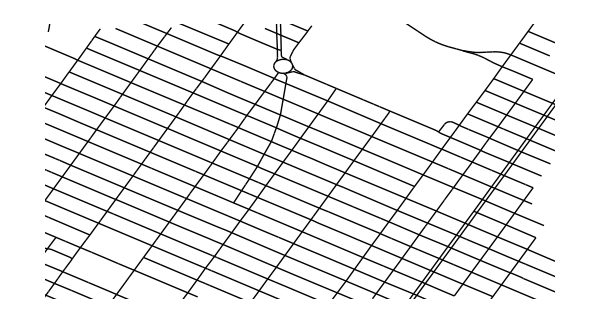

{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}

```mathematica
GeoGraphics[Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@Select[osmNewYork["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]];

generateLines[openStreetMapData_]:=Values[Line[Values[openStreetMapData[["Nodes",#Nodes,"Position"]]]]&/@Select[openStreetMapData["Ways"],MatchQ[#[["Tags","highway"]],"residential"|"primary"|"secondary"|"tertiary"|"motorway"|"trunk"]&]]/.
GeoPosition[{a_,b_}]:>{b,a}

Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600] (*cropped*)


ImagePartition[Graphics[generateLines[osmNewYork]/. GeoPosition[{lat_,lon_}]:>{lon,lat},PlotRange->{{-73.994,-73.968},{40.756,40.770}},(*your region bounds*)ImageSize->600]
, 75]
```

```mathematica
GeoGraphics[{Values[Line[Values[osmNewYork[["Nodes",#Nodes,"Position"]]]]&/@osmNewYork["Ways"]],GeoMarker[#["Position"]]&/@osmNewYork["Nodes"]}]
```

#### Applying the algorithm to the above data

```mathematica
(*1. Only closed highway ways*)closedWays=Select[osmNewYork["Ways"],Function[w,MatchQ[w["Tags","highway"],"residential"|"primary"|"secondary"|"tertiary"|"unclassified"]&&First[w["Nodes"]]===Last[w["Nodes"]]]]


polygons=Polygon[osmNewYork["Nodes",#["Nodes"],"Position"]]&/@closedWays;

nodes=osm["Nodes"];  (*This is already an Association*)

blockPolygons=Select[Table[Module[{nodeIDs,coords},nodeIDs=way["Nodes"];
If[AllTrue[nodeIDs,KeyExistsQ[nodes,#]&],coords=nodes[#]["Position"]&/@nodeIDs;
If[Length[coords]>=3,Polygon[coords],Nothing],Nothing]],{way,closedWays}],RegionQ]
```

<||>

{}

### Markov’s Chain

```mathematica
Check discord
```